```mathematica
Nt = 512; 
ti = 0; tf = 5; 
deltat = (tf - ti) /Nt ;
Nx = 128;
xi = -40; xf = 40; 
deltax = (xf - xi) / Nx; 
c =  1;

(*For Max Eigenvalue Plots*)
rs = Table[0.1*i,{i,1,200}];(*200 for Limits*)

maxevalsLD2 = Table[0,{i,1,Length[rs]}];
maxevalsRK2 = Table[0,{i,1,Length[rs]}];
maxevalsPI = Table[0,{i,1,Length[rs]}];



Subscript[δ, i_,j_]:=KroneckerDelta[i,j];

selectwidth = 3;
diffOrder = 4;
deriv = 2;


(*The total number of points in the stencil*)
totalpoints = (2*selectwidth) + 1;

(*The middle point in the stencil*)
middlepoint = selectwidth + 1;

(*Set up the grid for the stencil*)
grid=x0+(Range[totalpoints ]-middlepoint)Δx;

(LP=NDSolve`FiniteDifferenceDerivative[Derivative[deriv],grid,"DifferenceOrder"->diffOrder]@"DifferentiationMatrix"//Normal);
(LP2=NDSolve`FiniteDifferenceDerivative[Derivative[4],grid,"DifferenceOrder"->diffOrder - 2]@"DifferentiationMatrix"//Normal);
LP2 = LP.LP;

(*define r:=Δt/(Δx^deriv)*)
r=.;
LPX = LP*((-1)^deriv)*(r*(Δx)^deriv);
LPX2 = LP2*((-1)^4)*(r*(Δx)^4);

gn = (LPX[[middlepoint,All]]//Normal)//Simplify//FullSimplify;
LPX = Table[RotateRight[gn,i],{i,-selectwidth,selectwidth}];
LPX[[1,-1]]=0;
LPX[[1,-2]]=0;
LPX[[2,-1]]=0;
LPX[[-1,1]]=0;
LPX[[-1,2]]=0;
LPX[[-2,1]]=0;
LPX[[-3,1]] = 0;
LPX[[-2,2]] = 0;
LPX[[-1,3]] = 0;
LPX[[1,-3]] = 0;
LPX[[2,-2]] = 0;
LPX[[3,-1]] = 0;

gn2 = (LPX2[[middlepoint,All]]//Normal)//Simplify//FullSimplify;
LPX2 = Table[RotateRight[gn2,i],{i,-selectwidth,selectwidth}];
LPX2[[1,-1]]=0;
LPX2[[1,-2]]=0;
LPX2[[2,-1]]=0;
LPX2[[-1,1]]=0;
LPX2[[-1,2]]=0;
LPX2[[-2,1]]=0;
LPX2[[-3,1]] = 0;
LPX2[[-2,2]] = 0;
LPX2[[-1,3]] = 0;
LPX2[[1,-3]] = 0;
LPX2[[2,-2]] = 0;
LPX2[[3,-1]] = 0;


IP=IdentityMatrix[Length[LPX]];

(Mn=Inverse[IP-(ⅈ * LPX)/4  - LPX2/48 ].(IP+(ⅈ * LPX)/4- LPX2/48));

(*(Mn=Inverse[IP-(ⅈ * LPX)/4 ].(IP+(ⅈ * LPX)/4));*)

fn=(Mn[[middlepoint,All]]//Normal)//Simplify//FullSimplify;

(*Generate a M Matrix from the L matrix for the stencil*)
MP = Table[0,{i,1,Nx},{j,1,Nx}];

(*WITHOUT Periodic Boundary Conditions Placed*)
MP = Table[Sum[(Subscript[δ, i,j+(middlepoint-k)])fn[[k]] + (Subscript[δ, i,(j-k)])fn[[middlepoint + k]],{k,selectwidth}] + Subscript[δ, i,j] fn[[middlepoint]],{i,1,Nx},{j,1,Nx}];

(*WITH Periodic Boundary Conditions*)
(*MP = Table[Sum[(Subscript[δ, i,j+(middlepoint-k)])fn[[k]] + (Subscript[δ, i,(j-k)])fn[[middlepoint + k]],{k,selectwidth}] + Subscript[δ, i,j] fn[[middlepoint]] + Sum[(Subscript[δ, (i + Nx) - n,j])fn[[selectwidth - (n-1 )]] + (Subscript[δ, (i + Nx) + n,(j + 2*Nx)])fn[[(middlepoint + 1) + (n-1)]]  ,{n,1,selectwidth }],{i,1,Nx},{j,1,Nx}]//MatrixForm*)
```

```mathematica
(*(LP=NDSolve`FiniteDifferenceDerivative[Derivative[deriv],grid,"DifferenceOrder"->diffOrder]@"DifferentiationMatrix"//Normal);
(LP2=NDSolve`FiniteDifferenceDerivative[Derivative[4],grid,"DifferenceOrder"->diffOrder]@"DifferentiationMatrix"//Normal);*)
```

```mathematica
Do[
deltat = (deltax^2) * rs[[p]];

Xp= N[Table[xm = xi + m *deltax, {m, 0, Nx}],32];

T = N[Table[tn = ti + n *deltat, {n, 0, Nt -1 }],32];
Xo = N[Table[xn = xi + n *deltax, {n, 0, Nx -1}],32];

f[x_] = ⅇ^(- x^2+ⅈ x);


(************************************************************************************************************************)
(*Differentiation Matrix*)
(************************************************************************************************************************)
L1 = N[(NDSolve`FiniteDifferenceDerivative[Derivative[1],Xp,"DifferenceOrder"->1, PeriodicInterpolation->True]@"DifferentiationMatrix"//Normal),32];
L1//MatrixForm;
DL1 = N[-c * L1 * deltat,32];

L2 = N[Table[(NDSolve`FiniteDifferenceDerivative[Derivative[i],Xp, "DifferenceOrder"->2, PeriodicInterpolation->True]@"DifferentiationMatrix"//Normal), {i,1,8}],32];
DL2 = L2[[2]] * deltat * (ⅈ / 2);


(* LD2 *)
ILD2 = N[IdentityMatrix[Length[DL2]],32];
ALD2 = N[ILD2 - (DL2 / 2),32];
BLD2 = N[ILD2 + (DL2 / 2),32];
MLD2 = N[Inverse[ALD2].BLD2,32];

MMLD2 = MLD2;

Do[
MMLD2 = MMLD2.MMLD2;

,{i,1,10}];

evals = Eigenvalues[N[MMLD2]];

maxevalsLD2[[p]] = Max[Abs[evals]];

(*PI*)
MPtest = N[MP//.{N[r -> deltat / (deltax)^2,32]},32];

MMPI = MPtest;

Do[
MMPI = MMPI.MMPI;

,{i,1,10}];

evalsPI = Eigenvalues[N[MMPI]];

maxevalsPI[[p]] = Max[Abs[evalsPI]];

Print["Finished "<>ToString[rs[[p]]]];


,{p,1,Length[rs]}]


(*For Max Eigenvalue Plots*)
(*exportData=Flatten/@Transpose[{rsLD2,maxevalsLD2,rsEuler, maxevalsEuler, rsRK2, maxevalsRK2, rsRK4, maxevalsRK4, rsN, maxevalsN}];*)
(*Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\evals_max.dat",exportData,"Table"];*)
```

Finished 0.1

Finished 0.2

Finished 0.3

Finished 0.4

Finished 0.5

Finished 0.6

Finished 0.7

Finished 0.8

Finished 0.9

Finished 1.

Finished 1.1

Finished 1.2

Finished 1.3

Finished 1.4

Finished 1.5

Finished 1.6

Finished 1.7

Finished 1.8

Finished 1.9

Finished 2.

Finished 2.1

Finished 2.2

Finished 2.3

Finished 2.4

Finished 2.5

Finished 2.6

Finished 2.7

Finished 2.8

Finished 2.9

Finished 3.

Finished 3.1

Finished 3.2

Finished 3.3

Finished 3.4

Finished 3.5

Finished 3.6

Finished 3.7

Finished 3.8

Finished 3.9

Finished 4.

Finished 4.1

Finished 4.2

Finished 4.3

Finished 4.4

Finished 4.5

Finished 4.6

Finished 4.7

Finished 4.8

Finished 4.9

Finished 5.

Finished 5.1

Finished 5.2

Finished 5.3

Finished 5.4

Finished 5.5

Finished 5.6

Finished 5.7

Finished 5.8

Finished 5.9

Finished 6.

Finished 6.1

Finished 6.2

Finished 6.3

Finished 6.4

Finished 6.5

Finished 6.6

Finished 6.7

Finished 6.8

Finished 6.9

Finished 7.

Finished 7.1

Finished 7.2

Finished 7.3

Finished 7.4

Finished 7.5

Finished 7.6

Finished 7.7

Finished 7.8

Finished 7.9

Finished 8.

Finished 8.1

Finished 8.2

Finished 8.3

Finished 8.4

Finished 8.5

Finished 8.6

Finished 8.7

Finished 8.8

Finished 8.9

Finished 9.

Finished 9.1

Finished 9.2

Finished 9.3

Finished 9.4

Finished 9.5

Finished 9.6

Finished 9.7

Finished 9.8

Finished 9.9

Finished 10.

Finished 10.1

Finished 10.2

Finished 10.3

Finished 10.4

Finished 10.5

Finished 10.6

Finished 10.7

Finished 10.8

Finished 10.9

Finished 11.

Finished 11.1

Finished 11.2

Finished 11.3

Finished 11.4

Finished 11.5

Finished 11.6

Finished 11.7

Finished 11.8

Finished 11.9

Finished 12.

Finished 12.1

Finished 12.2

Finished 12.3

Finished 12.4

Finished 12.5

Finished 12.6

Finished 12.7

Finished 12.8

Finished 12.9

Finished 13.

Finished 13.1

Finished 13.2

Finished 13.3

Finished 13.4

Finished 13.5

Finished 13.6

Finished 13.7

Finished 13.8

Finished 13.9

Finished 14.

Finished 14.1

Finished 14.2

Finished 14.3

Finished 14.4

Finished 14.5

Finished 14.6

Finished 14.7

Finished 14.8

Finished 14.9

Finished 15.

Finished 15.1

Finished 15.2

Finished 15.3

Finished 15.4

Finished 15.5

Finished 15.6

Finished 15.7

Finished 15.8

Finished 15.9

Finished 16.

Finished 16.1

Finished 16.2

Finished 16.3

Finished 16.4

Finished 16.5

Finished 16.6

Finished 16.7

Finished 16.8

Finished 16.9

Finished 17.

Finished 17.1

Finished 17.2

Finished 17.3

Finished 17.4

Finished 17.5

Finished 17.6

Finished 17.7

Finished 17.8

Finished 17.9

Finished 18.

Finished 18.1

Finished 18.2

Finished 18.3

Finished 18.4

Finished 18.5

Finished 18.6

Finished 18.7

Finished 18.8

Finished 18.9

Finished 19.

Finished 19.1

Finished 19.2

Finished 19.3

Finished 19.4

Finished 19.5

Finished 19.6

Finished 19.7

Finished 19.8

Finished 19.9

Finished 20.

```mathematica
maxevalsLD2 = Join[{1},maxevalsLD2];
rsLD2 = Join[{0},rs];

maxevalsPI = Join[{1},maxevalsPI];
rsPI = Join[{0},rs];
```

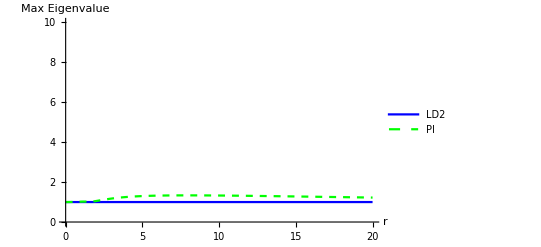

```mathematica
ListLinePlot[{Transpose[{rsLD2,maxevalsLD2^(1/1024)}],Transpose[{rsPI,maxevalsPI^(1/1024)}]},PlotStyle->{Blue, {Green, Dashed}}, PlotLegends->{"LD2", "PI"}, AxesLabel->{"r", "Max Eigenvalue"},PlotRange->{All,{0,10}}]
```

```mathematica
(*ListLinePlot[{Transpose[{rsLD2,maxevalsLD2}],Transpose[{rsPI,maxevalsPI}]},PlotStyle->{Blue, {Green, Dashed}}, PlotLegends->{"LD2", "PI"},PlotRange->{All,{.99,1.02}}, AxesLabel->{"r", "Max Eigenvalue"}]*)
```

```mathematica
(*ListLinePlot[{Transpose[{rsLD2,Abs[maxevalsLD2 - maxevalsPI]}]},PlotStyle->{Red}, PlotLegends->{"Difference in LD2 and PI"}, AxesLabel->{"r", "Difference in Max Eigenvalue"}]*)
```

```mathematica
(*MP//MatrixForm*)
```

```mathematica
maxevalsPI^(1/1024)
```

{1,1.00009,1.00066,1.00196,1.0038,1.00553,1.00634,1.00574,1.01006,1.01494,1.01906,1.02187,1.02298,1.02237,1.02662,1.03028,1.0333,1.03564,1.03735,1.04119,1.05412,1.06729,1.08053,1.09368,1.10662,1.11928,1.13157,1.14345,1.15488,1.16585,1.17633,1.18633,1.19584,1.20487,1.21344,1.22155,1.22921,1.23646,1.2433,1.24975,1.25582,1.26154,1.26693,1.27199,1.27675,1.28121,1.28541,1.28934,1.29303,1.29649,1.29973,1.30275,1.30558,1.30823,1.31069,1.31299,1.31513,1.31712,1.31897,1.32068,1.32226,1.32372,1.32507,1.32631,1.32744,1.32847,1.32941,1.33026,1.33103,1.33171,1.33232,1.33285,1.33332,1.33372,1.33405,1.33432,1.33454,1.33469,1.3348,1.33486,1.33486,1.33482,1.33474,1.33461,1.33445,1.33424,1.334,1.33372,1.3334,1.33306,1.33268,1.33227,1.33183,1.33136,1.33087,1.33035,1.3298,1.32924,1.32864,1.32803,1.3274,1.32674,1.32606,1.32537,1.32466,1.32393,1.32318,1.32241,1.32163,1.32084,1.32003,1.31921,1.31837,1.31752,1.31665,1.31578,1.31489,1.31399,1.31308,1.31216,1.31123,1.3103,1.30935,1.30839,1.30742,1.30645,1.30547,1.30448,1.30348,1.30247,1.30146,1.30044,1.29942,1.29839,1.29735,1.29631,1.29527,1.29421,1.29316,1.2921,1.29103,1.28996,1.28889,1.28781,1.28673,1.28565,1.28456,1.28347,1.28238,1.28128,1.28018,1.27908,1.27798,1.27688,1.27577,1.27466,1.27355,1.27244,1.27133,1.27022,1.2691,1.26799,1.26687,1.26575,1.26464,1.26352,1.2624,1.26128,1.26016,1.25904,1.25792,1.25681,1.25569,1.25457,1.25345,1.25234,1.25122,1.2501,1.24899,1.24788,1.24676,1.24565,1.24454,1.24343,1.24233,1.24122,1.24011,1.23901,1.23791,1.23681,1.23571,1.23461,1.23352,1.23243,1.23133,1.23025,1.22916,1.22807,1.22699,1.22591,1.22483}